# Tahm — PS 14

# Chapter 35

```mathematica
Interpreter["Location"]["Eiffel Tower"]
```

GeoPosition[{48.8583,2.29444}]

```mathematica
Interpreter["University"]["U of T"]
```

University of Toronto

```mathematica
Interpreter["Chemical"][{"C2H4","C2H6","C3H8"}]
```

{ethylene,ethane,propane}

```mathematica
Interpreter["Date"]["20140108"]
```

Wed 8 Jan 2014

```mathematica
Cases[Interpreter["University"][StringJoin["U of ",#]&/@ToUpperCase[Alphabet[]]],_Entity]
```

{University of Birjand,University of California-Berkeley,The University of Edinburgh,University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,University of Lethbridge,University of Michigan-Ann Arbor,University of Phoenix-Online Campus,University of Regina,University of Saskatchewan,University of Toronto}

```mathematica
Cases[Interpreter["Movie"][CommonName/@EntityClass["City","UnitedStatesCapitals"]],_Entity]
```

CommonName::noent: City is not an entity.

CommonName::noent: UnitedStatesCapitals is not an entity.

{}

```mathematica
Cases[Interpreter["City"][StringJoin/@Permutations[{"l","i","m","a"}]],_Entity]
```

{Lima,Lamai,Lami,Ilam,Balm,Mali,Milah,Mali,Alim,Amli}

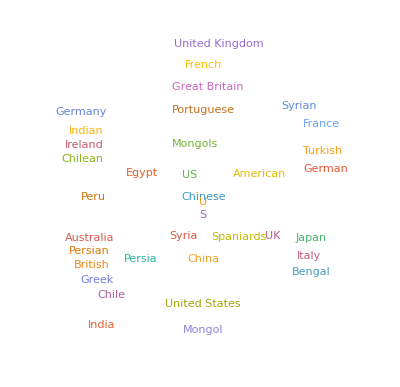

```mathematica
WordCloud[TextCases[WikipediaData["gunpowder"],"Country"]]
```

```mathematica
TextCases["She sells seashells by the sea shore","Noun"]
```

{seashells,sea,shore}

```mathematica
Length[TextCases[StringTake[WikipediaData["computers"],1000],#]]&/@{"Noun","Verb","Adjective"}
```

{54,23,20}

```mathematica
TextStructure[First[TextSentences[WikipediaData["computers"]]]]
```

A
Determinercomputer
Noun
Noun Phrase  is
Verb    a
Determinermachine
Noun
Noun Phrase    that
Wh-Determiner
Wh-Noun Phrase  can
Verb  be
Verb  programmed
Verb    to
Preposition    automatically
Adverb
Adverb Phrasecarry
Verb  out
Particle
Particle    sequences
Noun
Noun Phrase  of
Preposition      arithmetic
Adjectiveor
Conjunctionlogical
Adjective
Adjective Phraseoperations
Noun
Noun Phrase  (
Punctuation  computation
Noun
Noun Phrase)
Punctuation
Parenthetical
Noun Phrase
Prepositional Phrase
Noun Phrase
Verb Phrase
Verb Phrase
Clause
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Noun Phrase
Verb Phrase.
Punctuation
Sentence

```mathematica
TakeLargest[Counts[TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"]],10]
```

<|Rabbit→30,door→23,voice→22,time→21,way→20,Mouse→20,moment→18,thing→17,head→16,table→14|>

```mathematica
CommunityGraphPlot[First[TextStructure[First[TextSentences[WikipediaData["language"]]],"ConstituentGraphs"]],ChartLabels->Automatic]
```

-Graphics-

```mathematica
Length[TextCases[WordList[],#]]&/@{"Noun","Verb","Adjective","Adverb"}
```

{39176,39176,39176,39176}

```mathematica
Flatten[Table[WordTranslation[IntegerName[x],"French"],{x,2,10}]]
```

{deux,trois,quatre,cinq,six,sept,huit,neuf,dix}

# Chapter 36

```mathematica
CloudPublish[Style[RandomInteger[1000],100]]
```

CloudObject[https://www.wolframcloud.com/obj/a79816d5-8a25-4682-9764-5399cf8f7fea]

```mathematica
SystemOpen[CloudObject["https://www.wolframcloud.com/obj/fbc2dac1-7c4b-4178-bea6-15e0e2a22abe"]⟦1⟧]
```

```mathematica
CloudPublish[FormFunction[{"x"->"Number"},#x^#x&]]
```

CloudObject[https://www.wolframcloud.com/obj/6ac6f569-fa03-4966-a040-d1a5a2d16269]

```mathematica
CloudPublish[FormFunction[{"x"->"Number","y"->"Number"},#x*#y&]]
```

CloudObject[https://www.wolframcloud.com/obj/b6102ecd-4edc-48ec-b760-974b78c8a91a]

```mathematica
CloudPublish[FormFunction[{"topic"->"String"},WordCloud[WikipediaData[#topic]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/845bd237-34b9-44ba-bc80-32d41485b48b]

```mathematica
CloudPublish[FormPage[{"String"->"String"},Style[StringReverse[#String],50]&]]
```

CloudObject[https://www.wolframcloud.com/obj/96717d81-cb6f-4728-8047-5e1cfddee9ee]

```mathematica
CloudPublish[FormPage[{"N"->"Integer"}, Graphics[Style[RegularPolygon[#N],RandomColor[]]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/c859808f-5c2c-4239-af61-0844773c9ff1]

```mathematica
CloudPublish[FormPage[{"Location"->"Location","number"->"Integer"},GeoListPlot[GeoNearest["Volcano",#Location,#number]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/6e772891-fa09-41bc-bc0e-43064b361e48]